```mathematica
<<xlr8r.m
```

xCellerator 0.88 (18-July-2012) loaded 19 July 2012 at 16:24 GMT-06:60 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 1203-002)
GNU General Public License (GPL) Terms Apply.

```mathematica
lowLevelReactions[{{Overscript[A⇄B, ℰ],Subscript[k, 1],Subscript[k, 2],Subscript[k, 3]}}]
```

{{A+ℰ→Bind[A,ℰ],k_1},{Bind[A,ℰ]→A+ℰ,k_2},{Bind[A,ℰ]→B+ℰ,k_3}}

```mathematica
model={{Underoverscript[X⇄XP⇄XPP, ZPP, Z],a,d,k,a,d,k},
{Underoverscript[Y⇄YP⇄YPP, XPP, X],a,d,k,a,d,k},  {Underoverscript[Z⇄ZP⇄ZPP, YPP, Y],a,d,k,a,d,k}};
```

```mathematica
interpret[model]
```

{{X'[t]==-a X[t] Y[t]-a X[t] YP[t]-a X[t] Z[t]+d Bind[X,Y][t]+k Bind[X,Y][t]+d Bind[X,YP][t]+k Bind[X,YP][t]+d Bind[X,Z][t]+k Bind[XP,ZPP][t],XP'[t]==-a XP[t] Z[t]-a XP[t] ZPP[t]+k Bind[X,Z][t]+d Bind[XP,Z][t]+d Bind[XP,ZPP][t]+k Bind[XPP,ZPP][t],XPP'[t]==-a XPP[t] YP[t]-a XPP[t] YPP[t]-a XPP[t] ZPP[t]+k Bind[XP,Z][t]+d Bind[XPP,YP][t]+k Bind[XPP,YP][t]+d Bind[XPP,YPP][t]+k Bind[XPP,YPP][t]+d Bind[XPP,ZPP][t],Y'[t]==-a X[t] Y[t]-a Y[t] Z[t]-a Y[t] ZP[t]+d Bind[X,Y][t]+k Bind[XPP,YP][t]+d Bind[Y,Z][t]+k Bind[Y,Z][t]+d Bind[Y,ZP][t]+k Bind[Y,ZP][t],YP'[t]==-a X[t] YP[t]-a XPP[t] YP[t]+k Bind[X,Y][t]+d Bind[X,YP][t]+d Bind[XPP,YP][t]+k Bind[XPP,YPP][t],YPP'[t]==-a XPP[t] YPP[t]-a YPP[t] ZP[t]-a YPP[t] ZPP[t]+k Bind[X,YP][t]+d Bind[XPP,YPP][t]+d Bind[YPP,ZP][t]+k Bind[YPP,ZP][t]+d Bind[YPP,ZPP][t]+k Bind[YPP,ZPP][t],Z'[t]==-a X[t] Z[t]-a XP[t] Z[t]-a Y[t] Z[t]+d Bind[X,Z][t]+k Bind[X,Z][t]+d Bind[XP,Z][t]+k Bind[XP,Z][t]+d Bind[Y,Z][t]+k Bind[YPP,ZP][t],ZP'[t]==-a Y[t] ZP[t]-a YPP[t] ZP[t]+k Bind[Y,Z][t]+d Bind[Y,ZP][t]+d Bind[YPP,ZP][t]+k Bind[YPP,ZPP][t],ZPP'[t]==-a XP[t] ZPP[t]-a XPP[t] ZPP[t]-a YPP[t] ZPP[t]+d Bind[XP,ZPP][t]+k Bind[XP,ZPP][t]+d Bind[XPP,ZPP][t]+k Bind[XPP,ZPP][t]+k Bind[Y,ZP][t]+d Bind[YPP,ZPP][t],Bind[X,Y]'[t]==a X[t] Y[t]-d Bind[X,Y][t]-k Bind[X,Y][t],Bind[X,YP]'[t]==a X[t] YP[t]-d Bind[X,YP][t]-k Bind[X,YP][t],Bind[X,Z]'[t]==a X[t] Z[t]-d Bind[X,Z][t]-k Bind[X,Z][t],Bind[XP,Z]'[t]==a XP[t] Z[t]-d Bind[XP,Z][t]-k Bind[XP,Z][t],Bind[XP,ZPP]'[t]==a XP[t] ZPP[t]-d Bind[XP,ZPP][t]-k Bind[XP,ZPP][t],Bind[XPP,YP]'[t]==a XPP[t] YP[t]-d Bind[XPP,YP][t]-k Bind[XPP,YP][t],Bind[XPP,YPP]'[t]==a XPP[t] YPP[t]-d Bind[XPP,YPP][t]-k Bind[XPP,YPP][t],Bind[XPP,ZPP]'[t]==a XPP[t] ZPP[t]-d Bind[XPP,ZPP][t]-k Bind[XPP,ZPP][t],Bind[Y,Z]'[t]==a Y[t] Z[t]-d Bind[Y,Z][t]-k Bind[Y,Z][t],Bind[Y,ZP]'[t]==a Y[t] ZP[t]-d Bind[Y,ZP][t]-k Bind[Y,ZP][t],Bind[YPP,ZP]'[t]==a YPP[t] ZP[t]-d Bind[YPP,ZP][t]-k Bind[YPP,ZP][t],Bind[YPP,ZPP]'[t]==a YPP[t] ZPP[t]-d Bind[YPP,ZPP][t]-k Bind[YPP,ZPP][t]},{X,XP,XPP,Y,YP,YPP,Z,ZP,ZPP,Bind[X,Y],Bind[X,YP],Bind[X,Z],Bind[XP,Z],Bind[XP,ZPP],Bind[XPP,YP],Bind[XPP,YPP],Bind[XPP,ZPP],Bind[Y,Z],Bind[Y,ZP],Bind[YPP,ZP],Bind[YPP,ZPP]}}

```mathematica
lowLevelReactions[model]
```

{{X+Z→Bind[X,Z],a},{Bind[X,Z]→X+Z,d},{Bind[X,Z]→XP+Z,k},{XP+ZPP→Bind[XP,ZPP],a},{Bind[XP,ZPP]→XP+ZPP,d},{Bind[XP,ZPP]→X+ZPP,k},{XP+Z→Bind[XP,Z],a},{Bind[XP,Z]→XP+Z,d},{Bind[XP,Z]→XPP+Z,k},{XPP+ZPP→Bind[XPP,ZPP],a},{Bind[XPP,ZPP]→XPP+ZPP,d},{Bind[XPP,ZPP]→XP+ZPP,k},{X+Y→Bind[X,Y],a},{Bind[X,Y]→X+Y,d},{Bind[X,Y]→X+YP,k},{XPP+YP→Bind[XPP,YP],a},{Bind[XPP,YP]→XPP+YP,d},{Bind[XPP,YP]→XPP+Y,k},{X+YP→Bind[X,YP],a},{Bind[X,YP]→X+YP,d},{Bind[X,YP]→X+YPP,k},{XPP+YPP→Bind[XPP,YPP],a},{Bind[XPP,YPP]→XPP+YPP,d},{Bind[XPP,YPP]→XPP+YP,k},{Y+Z→Bind[Y,Z],a},{Bind[Y,Z]→Y+Z,d},{Bind[Y,Z]→Y+ZP,k},{YPP+ZP→Bind[YPP,ZP],a},{Bind[YPP,ZP]→YPP+ZP,d},{Bind[YPP,ZP]→YPP+Z,k},{Y+ZP→Bind[Y,ZP],a},{Bind[Y,ZP]→Y+ZP,d},{Bind[Y,ZP]→Y+ZPP,k},{YPP+ZPP→Bind[YPP,ZPP],a},{Bind[YPP,ZPP]→YPP+ZPP,d},{Bind[YPP,ZPP]→YPP+ZP,k}}

```mathematica
lowLevelReactions[model]//Sort//TableForm
```

X+Y→Bind[X,Y] | a
X+YP→Bind[X,YP] | a
XPP+YP→Bind[XPP,YP] | a
XPP+YPP→Bind[XPP,YPP] | a
X+Z→Bind[X,Z] | a
XP+Z→Bind[XP,Z] | a
Y+Z→Bind[Y,Z] | a
Y+ZP→Bind[Y,ZP] | a
YPP+ZP→Bind[YPP,ZP] | a
XP+ZPP→Bind[XP,ZPP] | a
XPP+ZPP→Bind[XPP,ZPP] | a
YPP+ZPP→Bind[YPP,ZPP] | a
Bind[X,Y]→X+Y | d
Bind[X,Y]→X+YP | k
Bind[X,YP]→X+YP | d
Bind[X,YP]→X+YPP | k
Bind[X,Z]→X+Z | d
Bind[X,Z]→XP+Z | k
Bind[XP,Z]→XP+Z | d
Bind[XP,Z]→XPP+Z | k
Bind[XP,ZPP]→X+ZPP | k
Bind[XP,ZPP]→XP+ZPP | d
Bind[XPP,YP]→XPP+Y | k
Bind[XPP,YP]→XPP+YP | d
Bind[XPP,YPP]→XPP+YP | k
Bind[XPP,YPP]→XPP+YPP | d
Bind[XPP,ZPP]→XP+ZPP | k
Bind[XPP,ZPP]→XPP+ZPP | d
Bind[Y,Z]→Y+Z | d
Bind[Y,Z]→Y+ZP | k
Bind[Y,ZP]→Y+ZP | d
Bind[Y,ZP]→Y+ZPP | k
Bind[YPP,ZP]→YPP+Z | k
Bind[YPP,ZP]→YPP+ZP | d
Bind[YPP,ZPP]→YPP+ZP | k
Bind[YPP,ZPP]→YPP+ZPP | d

```mathematica
IC={X-> 1, Y-> 1.5, Z-> 2};
R={a-> 1, d-> 1, k-> 1};
s=run[model,timeSpan-> 150, initialConditions-> IC,rates-> R];
```

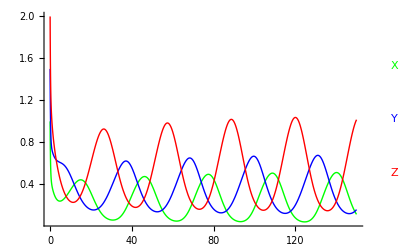

```mathematica
runPlot[s,{X,Y,Z}]
```